### Forward calculation

```mathematica
(* Model densitas energi konstan *)
ϵ[p_]=
240.; 
dϵdp=D[ϵ[p],p];
(* Model LinEoS *)
```

```mathematica
eq1[r_]=(4 π r^3 p[r]+m[r])(2GS)/(2 r (r-2 GS m[r]));
(*Persamaan differensial metrik*)
eq2[r_]=-m'[r]+4 π r^2 ϵ[p[r]];(*Persamaan differensial massa*)
eq3[r_]=-p'[r]- eq1[r](ϵ[p[r]]+p[r]) ; (*Persamaan TOV*)
```

```mathematica
GS=1.325*10^-12; (* Konstanta gravitasi *)
MSS= 1.1155 * 10^15; (* Massa matahari *)
r0=10^(-3);(* radius di pusat *)
rmax=100000.;
MCC=1 *10^-9; (* Massa di pusat *)
PCC=300; (* Tekanan di pusat *)
```

```mathematica
Clear[rStar];
state=First[NDSolve`ProcessEquations[{eq2[r]==0,eq3[r]==0,m[r0]==MCC , p[r0]==PCC},{m,p},{r,r0,rmax},Method->{"EventLocator","Event" :>{p[r]},"EventAction":>Throw[rStar=r,"StopIntegration"]}]];
NDSolve`Iterate[state,rmax]
solf=NDSolve`ProcessSolutions[state]
rStar
```

{m→InterpolatingFunction[{{0.001, 17062.9}}, <>],p→InterpolatingFunction[{{0.001, 17062.9}}, <>]}

17062.9

17062.88829323245     4.477008501499378     240.     300

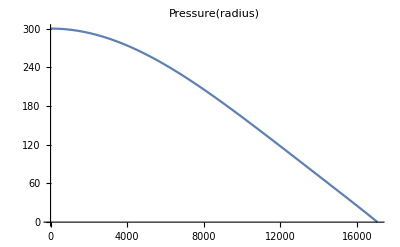

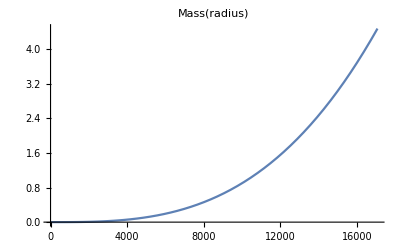

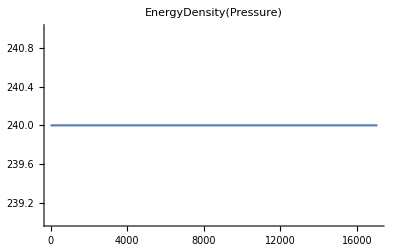

```mathematica
mo[r_]=Evaluate[m[r]/. solf];
po[r_]=Evaluate[p[r]/. solf];
mStar=mo[rStar];
(*Print[rStar,"     ",mStar/MSS,"     ",ϵ[p[r0]],"     ",PCC]*)
Print[FortranForm[rStar],"     ",FortranForm[mo[rStar]/MSS],"     ",ϵ[po[r0]],"     ",PCC]
Plot[{po[r]},{r,r0,rStar},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{mo[r]/MSS},{r,r0,rStar},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{ϵ[po[r]]},{r,r0,rStar},PlotRange->All,PlotLabel->EnergyDensity[Pressure]]
```

```mathematica
{rStar,mo[rStar],po[rStar]}
{r0,po[r0],mo[r0]}
{1-2GS mo[rStar]/rStar}
```

{17062.9,4.9941×10^15,3.06422×10^-14}

{1/1000,300.,1.×10^-9}

{0.224377}

### Reverse calculation

```mathematica
(* Model densitas energi konstan *)
ϵ[p_]=
240.; 
dϵdp=D[ϵ[p],p];
(* Model LinEoS *)
```

```mathematica
eq1[r_]=(4 π r^3 p[r]+m[r])(2GS)/(2 r (r-2 GS m[r]));
(*Persamaan differensial metrik*)
eq2[r_]=-m'[r]+4 π r^2 ϵ[p[r]];(*Persamaan differensial massa*)
eq3[r_]=-p'[r]- eq1[r](ϵ[p[r]]+p[r]) ; (*Persamaan TOV*)
```

```mathematica
GS=1.325*10^-12; (* Konstanta gravitasi *)
MSS= 1.1155 * 10^15; (* Massa matahari *)
rmax=10^(-3);
r0=rStar;(* radius di permukaan *)
MCC=mo[rStar]; (* Massa di permukaan *)
PCC=po[rStar]; (* Tekanan di permukaan *)
```

```mathematica
Clear[rStar2];
state=First[NDSolve`ProcessEquations[{eq2[r]==0,eq3[r]==0,m[r0]==MCC , p[r0]==PCC},{m,p},{r,r0,rmax},Method->{"EventLocator","Event" :>{r},"EventAction":>Throw[rStar2=r,"StopIntegration"]}]];
NDSolve`Iterate[state,rmax]
solb=NDSolve`ProcessSolutions[state]
rStar
```

{m→InterpolatingFunction[{{0.001, 17062.9}}, <>],p→InterpolatingFunction[{{0.001, 17062.9}}, <>]}

17062.9

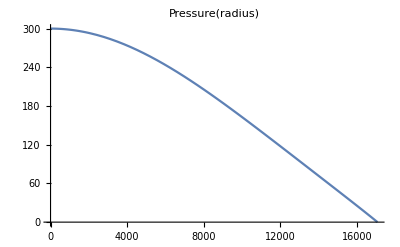

-Graphics-

-Graphics-

```mathematica
moo[r_]=Evaluate[m[r]/. solb];
poo[r_]=Evaluate[p[r]/. solb];
mStar=moo[rStar];
Plot[{poo[r]},{r,rmax,r0},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{moo[r]/MSS},{r,rmax,r0},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{ϵ[poo[r]]},{r,rmax,r0},PlotRange->All,PlotLabel->EnergyDensity[Pressure]]
```

```mathematica
{r0,moo[r0],poo[r0]}
{rmax,poo[rmax],moo[rmax]}
1-2GS moo[r0]/r0
```

{17062.9,4.9941×10^15,3.06422×10^-14}

{1/1000,300.05,69104.8}

0.224377

Catatan : saat densitas energi konstan, hasil integrasi forward = backward

### Perbandingan

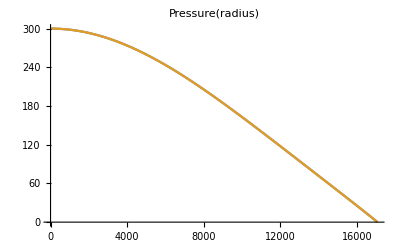

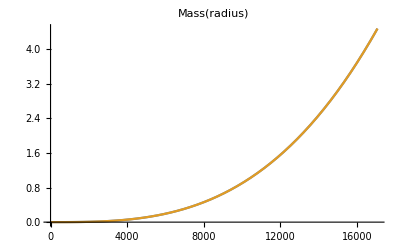

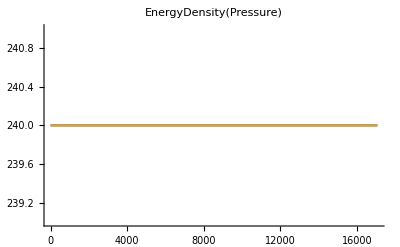

```mathematica
Plot[{po[r],poo[r]},{r,rmax,r0},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{mo[r]/MSS,moo[r]/MSS},{r,rmax,r0},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{ϵ[po[r]],ϵ[poo[r]]},{r,rmax,r0},PlotRange->All,PlotLabel->EnergyDensity[Pressure]]
```